```mathematica
B[s]=a[s] Cos[2 ∫√η[s] ⅆs]+c[s];
D[B[s],s];
D[B[s],{s,2}];
D[B[s],{s,3}];
```

```mathematica
D[B[s],{s,3}]+4 η[s] D[B[s],{s,1}]+2 D[η[s],{s,1}] B[s]
```

4 η[s] (-2 a[s] Sin[2 ∫√η[s]ⅆs] √η[s]+Cos[2 ∫√η[s]ⅆs] a'[s]+c'[s])+2 (c[s]+a[s] Cos[2 ∫√η[s]ⅆs]) η'[s]+3 a'[s] (-4 Cos[2 ∫√η[s]ⅆs] η[s]-(Sin[2 ∫√η[s]ⅆs] η'[s])/(√η[s]))-6 Sin[2 ∫√η[s]ⅆs] √η[s] a''[s]+a[s] (8 Sin[2 ∫√η[s]ⅆs] η[s]^(3/2)-6 Cos[2 ∫√η[s]ⅆs] η'[s]+(Sin[2 ∫√η[s]ⅆs] η'[s]^2)/(2 η[s]^(3/2))-(Sin[2 ∫√η[s]ⅆs] η''[s])/(√η[s]))+Cos[2 ∫√η[s]ⅆs] a^(3)[s]+c^(3)[s]

```mathematica
FullSimplify[%]
```

4 η[s] c'[s]+2 c[s] η'[s]+(Sin[2 ∫√η[s]ⅆs] (a[s] η'[s]^2-12 η[s]^2 a''[s]-2 η[s] (3 a'[s] η'[s]+a[s] η''[s])))/(2 η[s]^(3/2))+Cos[2 ∫√η[s]ⅆs] (-8 η[s] a'[s]-4 a[s] η'[s]+a^(3)[s])+c^(3)[s]

```mathematica
ap[s]=-(a[s] D[η[s],s])/(2 η[s]);
D[ap[s],s]
```

-(a'[s] η'[s])/(2 η[s])+(a[s] η'[s]^2)/(2 η[s]^2)-(a[s] η''[s])/(2 η[s])

```mathematica
a''[s]=a[s] ((3 η'[s]^2)/(4 η[s]^2)-η''[s]/(2 η[s]))
```

a[s] ((3 η'[s]^2)/(4 η[s]^2)-η''[s]/(2 η[s]))

```mathematica
a[s] η'[s]^2-12 η[s]^2 a''[s]-2 η[s] (3 a'[s] η'[s]+a[s] η''[s])
```

a[s] η'[s]^2-2 η[s] (3 a'[s] η'[s]+a[s] η''[s])-12 a[s] η[s]^2 ((3 η'[s]^2)/(4 η[s]^2)-η''[s]/(2 η[s]))

```mathematica
Simplify[a[s] η'[s]^2-2 η[s] (3 a'[s] η'[s]+a[s] η''[s])-12 a[s] η[s]^2 ((3 η'[s]^2)/(4 η[s]^2)-η''[s]/(2 η[s]))]
```

-8 a[s] η'[s]^2+η[s] (-6 a'[s] η'[s]+4 a[s] η''[s])

```mathematica
Clear[η]
sol=DSolve[{4 η''[s]==5 η'[s]/η[s],η[0]==1,η'[0]==-0.5},η[s],s,Assumptions->{s≥0,η∈Reals}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -1+InverseFunction[4/5 ⅇ^(-(4 C[1])/5) ExpIntegralEi[4/5 C[«1»]+Log[Slot[«1»]]]&][C[2]] == 0.

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{η[s]→InverseFunction[4/5 ⅇ^(-4 (-0.5)/5) ExpIntegralEi[(4 (-0.5))/5+Log[#1]]&][s+0.8 ⅇ^(-0.8 C[1]) ExpIntegralEi[0.8 C[1]]]}}

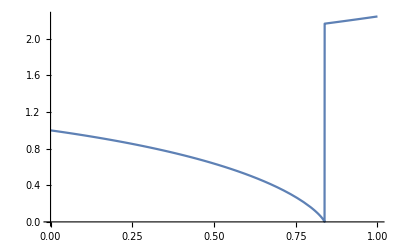

```mathematica
Plot[η[s]/.sol/.{C[1]->-0.5},{s, 0, 1}]
```

```mathematica
sol=NDSolve[{4 η''[s]-5 η'[s]/η[s]==0,η[0]==1,η'[0]==-0.5},η,{s,0,1}]
Plot[Evaluate[η[s]/.sol],{s,0,1},PlotRange->All]
```

NDSolve::ndsz: At s == 0.838262, step size is effectively zero; singularity or stiff system suspected.

{{η→InterpolatingFunction[{{0., 0.838262}}, <>]}}

-Graphics-

```mathematica
sol=DSolve[{β'''[s]+4 ⅇ^(-s^2/(2 σ^2)) β'[s]-(2 s)/σ^2 ⅇ^(-s^2/(2 σ^2)) β[s]==0,β[0]==1,β'[0]==0},β[s],s]
```

DSolve[{-(2 ⅇ^(-s^2/(2 σ^2)) s β[s])/σ^2+4 ⅇ^(-s^2/(2 σ^2)) β'[s]+β^(3)[s]==0,β[0]==1,β'[0]==0},β[s],s]

100

{{β→InterpolatingFunction[{{0., 1.}}, <>]}}

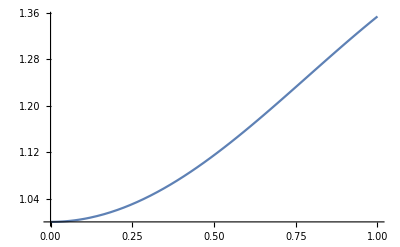

```mathematica
σ=100
sol=NDSolve[{β'''[s]+4 ⅇ^(-s^2/(2 σ^2)) β'[s]-(2 s)/σ^2 ⅇ^(-s^2/(2 σ^2)) β[s]==0,β[0]==1,β'[0]==0, β''[0]==1},β,{s,0,1}]
Plot[Evaluate[β[s]/.sol],{s,0,1},PlotRange->All]
```

```mathematica
sol=DSolve[{β'''[s]+4 (1-m s) β'[s]-2 m β[s]==0,β[0]==1,β'[0]==0},β[s],s]
```

{{β[s]→(AiryAiPrime[-1/m^(2/3)] AiryBi[-1/m^(2/3)] AiryBi[(-1+m s)/m^(2/3)]^2-2 AiryAi[(-1+m s)/m^(2/3)] AiryBi[-1/m^(2/3)] AiryBi[(-1+m s)/m^(2/3)] AiryBiPrime[-1/m^(2/3)]+AiryAi[-1/m^(2/3)] AiryBi[(-1+m s)/m^(2/3)]^2 AiryBiPrime[-1/m^(2/3)]+AiryAi[(-1+m s)/m^(2/3)]^2 AiryAiPrime[-1/m^(2/3)] AiryBi[-1/m^(2/3)]^3 C[1]-2 AiryAi[-1/m^(2/3)] AiryAi[(-1+m s)/m^(2/3)] AiryAiPrime[-1/m^(2/3)] AiryBi[-1/m^(2/3)]^2 AiryBi[(-1+m s)/m^(2/3)] C[1]+AiryAi[-1/m^(2/3)]^2 AiryAiPrime[-1/m^(2/3)] AiryBi[-1/m^(2/3)] AiryBi[(-1+m s)/m^(2/3)]^2 C[1]-AiryAi[-1/m^(2/3)] AiryAi[(-1+m s)/m^(2/3)]^2 AiryBi[-1/m^(2/3)]^2 AiryBiPrime[-1/m^(2/3)] C[1]+2 AiryAi[-1/m^(2/3)]^2 AiryAi[(-1+m s)/m^(2/3)] AiryBi[-1/m^(2/3)] AiryBi[(-1+m s)/m^(2/3)] AiryBiPrime[-1/m^(2/3)] C[1]-AiryAi[-1/m^(2/3)]^3 AiryBi[(-1+m s)/m^(2/3)]^2 AiryBiPrime[-1/m^(2/3)] C[1])/(AiryBi[-1/m^(2/3)]^2 (AiryAiPrime[-1/m^(2/3)] AiryBi[-1/m^(2/3)]-AiryAi[-1/m^(2/3)] AiryBiPrime[-1/m^(2/3)]))}}

```mathematica
Solve[a^3 m (m-1) (m-2)+4 a m-4 a==0,m]
```

{{m→1},{m→(a^2-√(-4 a^2+a^4))/a^2},{m→(a^2+√(-4 a^2+a^4))/a^2}}

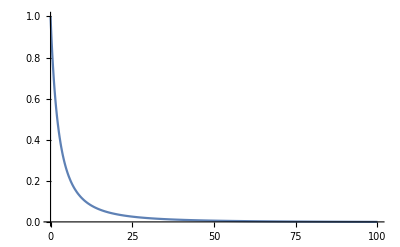

```mathematica
Plot[1/(1+0.2 s)^2,{s, 0, 100},PlotRange->Full]
```

0.2

2

-0.5+0.0502519 ⅈ

-0.5-0.0502519 ⅈ

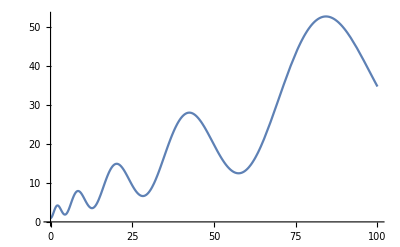

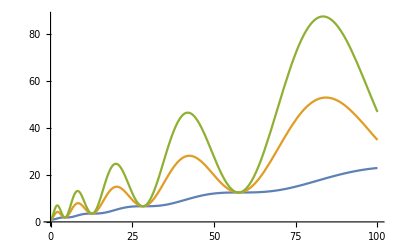

```mathematica
a=.2
c1=2
cp=1/2-1/2 c1-1/(2 √(1-4/a^2))
cm=1/2-1/2 c1+1/(2 √(1-4/a^2))
Bce[s_]:=c1 (1+a s)+cp (1+a s)^(1+√(1-4/a^2))+cm (1+a s)^(1-√(1-4/a^2))
Br[s_,c1_]:=(1+a s) (c1+(1-c1) Cos[Log[1+a s] √(4/a^2-1)]-1/(√(4/a^2-1)) Sin[Log[1+a s] √(4/a^2-1)])
Plot[{Bce[s]},{s,0,100}]
Plot[{Br[s,1],Br[s,2],Br[s,3]},{s,0,100}]
```

```mathematica
Clear[a,c1]
Br[s_]=(1+a s) (c1+(1-c1) Cos[Log[1+a s] √(4/a^2-1)]-1/(√(4/a^2-1)) Sin[Log[1+a s] √(4/a^2-1)]);
Simplify[Br'''[s]+4/(1+a s)^2 Br'[s]-(4 a)/(1+a s)^3 Br[s]]==0
```

True

```mathematica
Clear[a,c1,cp,cm]
mp=1+√(1-4/a^2);
mn=1-√(1-4/a^2);
Bt[s_]=c1 (1+a s)+cp (1+a s)^mp+cm (1+a s)^mn;
Simplify[(1+a s)^3 Bt'''[s]+4 (1+a s) Bt'[s]-4 a Bt[s]]
```

0

```mathematica
Br[s_]=(1+a s) (1+1/(4/a^2-1)-1/(4/a^2-1) Cos[Log[1+a s] √(4/a^2-1)]-1/(√(4/a^2-1)) Sin[Log[1+a s] √(4/a^2-1)]);
Simplify[1/2 Br''[s]+1/(1+a s)^2 Br[s]-1/Br[s] (1+(Br'[s]/2)^2)]==0
```

True

```mathematica
Simplify[1/2 Bt''[s]+1/(1+a s)^2 Bt[s]-1/Bt[s] (1+(Bt'[s]/2)^2)]==0
```

(-(-4+a^2) c1^2+4 (-1+(-4+a^2) cm cp))/(4 (c1+a c1 s+cm (1+a s)^(1-√(1-4/a^2))+cp (1+a s)^(1+√(1-4/a^2))))==0

```mathematica
Solve[-(-4+a^2) c1^2+4 (-1+(-4+a^2) cm cp)==0,c1]
```

{{c1→-(2 √(-1-4 cm cp+a^2 cm cp))/(√(-4+a^2))},{c1→(2 √(-1-4 cm cp+a^2 cm cp))/(√(-4+a^2))}}

```mathematica
mp=1+ⅈ √(4/a^2-1);
mn=1-ⅈ √(4/a^2-1);
Bt[s_]=(2 √(-1-4 cm cp+a^2 cm cp))/(√(-4+a^2)) (1+a s)+cp (1+a s)^mp+cm (1+a s)^mn;
cm=c1-ⅈ c2;
cp=c1+ⅈ c2;
```

```mathematica
FullSimplify[Bt[s],Assumptions->{a<2,a>0,a∈Reals}]
```

(1+a s) ((2 √(-1+(-4+a^2) c1^2+(-4+a^2) c2^2))/(√(-4+a^2))+(c1-ⅈ c2) (1+a s)^(-ⅈ √(-1+4/a^2))+(c1+ⅈ c2) (1+a s)^(ⅈ √(-1+4/a^2)))

```mathematica
Simplify[√((1-a^2/4+(1-a^2/4) (4/a^2-1)+(4/a^2-1)^2)/((4/a^2-1)^2 (1-a^2/4)))]
```

4 √(1/((-4+a^2)^2))

```mathematica
Bq[s_]=(1+a s) (-√(c1^2+c2^2+1/(1-a^2/4))+c1 Cos[Log[1+a s] √(4/a^2-1)]+c2 Sin[Log[1+a s] √(4/a^2-1)]);
sol=Solve[{Bq[0]==β0,Bq'[0]==-2 α0},{c1,c2}]
```

{{c1→(-1/(2-a)-1/(2+a)-α0^2/(2-a)-α0^2/(2+a)-(2 α0 β0)/(2-a)+(2 α0 β0)/(2+a)+2 β0^2-β0^2/(2-a)-β0^2/(2+a))/(2 β0),c2→-(√((4-a^2)/a^2) α0)/(2-a)+(√((4-a^2)/a^2) α0)/(2+a)+√((4-a^2)/a^2) β0-(√((4-a^2)/a^2) β0)/(2-a)-(√((4-a^2)/a^2) β0)/(2+a)}}

```mathematica
FullSimplify[c1/.sol]
```

{(2+2 α0^2+2 a α0 β0+(-2+a^2) β0^2)/((-4+a^2) β0)}

```mathematica
FullSimplify[c2/.sol]
```

{(√(-1+4/a^2) a (2 α0+a β0))/(-4+a^2)}

{a→1.5,β0→1}

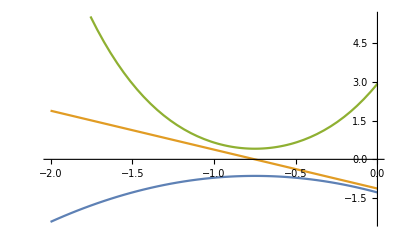

```mathematica
const={a->1.5,β0->1}
Plot[{(2+2 α0^2+2 a α0 β0+(-2+a^2) β0^2)/((-4+a^2) β0)/.const,(√(-1+4/a^2) a (2 α0+a β0))/(-4+a^2)/.const,((2+2 α0^2+2 a α0 β0+(-2+a^2) β0^2)/((-4+a^2) β0))^2+((√(-1+4/a^2) a (2 α0+a β0))/(-4+a^2))^2/.const},{α0, -2, 0}]
```

```mathematica
FullSimplify[((2+2 α0^2+2 a α0 β0+(-2+a^2) β0^2)/((-4+a^2) β0))^2+((√(-1+4/a^2) a (2 α0+a β0))/(-4+a^2))^2/.{β0->1}]
```

(4 (a^2+4 a α0+(4+a^2) α0^2+2 a α0^3+α0^4))/((-4+a^2)^2)

```mathematica
FullSimplify[(4 (a^2+4 a α0+(4+a^2) α0^2+2 a α0^3+α0^4))/((-4+a^2)^2)/.α0->-a/2]
```

a^4/(4 (-4+a^2)^2)

```mathematica
FullSimplify[D[(4 (a^2+4 a α0+(4+a^2) α0^2+2 a α0^3+α0^4))/((-4+a^2)^2),α0]]
```

(8 (a+2 α0) (2+α0 (a+α0)))/((-4+a^2)^2)

```mathematica
FullSimplify[√(a^4/(4 (a^2-4)^2)+1/(1-a^2/4))]
```

1/2 √(((-8+a^2)^2)/((-4+a^2)^2))

```mathematica
FullSimplify[1/2 (a^2-8)/(a^2-4)-1]
```

a^2/(8-2 a^2)

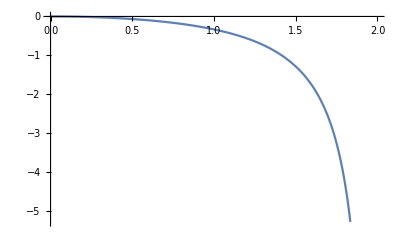

```mathematica
Plot[a^2/(a^2-4),{a,0,2}]
```

```mathematica
FullSimplify[1/((4/a^2-1)^2)+1/(4/a^2-1)]
```

(4 a^2)/((-4+a^2)^2)

```mathematica
FullSimplify[(2 a)/(-4+a^2)-1/(4/a^2-1)]
```

a/(-2+a)

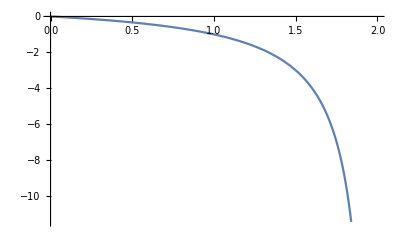

```mathematica
Plot[a/(-2+a),{a,0,2}]
```

```mathematica
Solve[a/(-2+a)==-0.1,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.181818}}

```mathematica
a/(-2+a)/.a->0.25
```

-0.142857

```mathematica
FullSimplify[√((4 (a^2+4 a α0+(4+a^2) α0^2+2 a α0^3+α0^4))/((-4+a^2)^2)+1/(1-a^2/4))+√((4 (a^2+4 a α0+(4+a^2) α0^2+2 a α0^3+α0^4))/((-4+a^2)^2))]
```

2 (√((a^2+4 a α0+(4+a^2) α0^2+2 a α0^3+α0^4)/((-4+a^2)^2))+√((2+α0 (a+α0))^2/((-4+a^2)^2)))